```mathematica
maxOrder=8;
RealSphericalHarmonicY[l_,m_,θ_,ϕ_]:=If[m<0,
ⅉ/Sqrt[2](SphericalHarmonicY[l,m,θ,ϕ]-(-1)^m SphericalHarmonicY[l,-m,θ,ϕ]),
If[m==0,
SphericalHarmonicY[l,m,θ,ϕ],
1/Sqrt[2](SphericalHarmonicY[l,m,θ,ϕ]+(-1)^m SphericalHarmonicY[l,-m,θ,ϕ])
]
]
ToMultiIndex[coefficient_,powers_]:=If[powers=={},
{},
Total@(UnitVector[3,#]&/@powers)->coefficient]
CoefficientArraysToMultiIndex[array_]:=If[Length@array==1,
<|{0,0,0}->array[[1]]|>,
Association@Select[Flatten@Select[MapIndexed[ToMultiIndex,#,{Length@Dimensions@#}]&/@array,Length@#>0&]/.(index_->0):>{},Length@#>0&]];
dr=dx Sin[θ]Cos[ϕ]+dy Sin[θ]Sin[ϕ]+dz Cos[θ];
sphericalToCartesian=Table[{l,m}->4π(-1)^l/1^(l+1)
CoefficientArraysToMultiIndex[CoefficientArrays[(dx^2+dy^2+dz^2)^(l/2)Simplify@TrigExpand@ExpToTrig@TransformedField[
"Spherical"->"Cartesian",
RealSphericalHarmonicY[l,m,θ,ϕ],
{ρ,θ,ϕ}->{dx,dy,dz}
],{dx,dy,dz}]],
{l,0,maxOrder},{m,-l,l}]//Association;
```

```mathematica
toExport=Association@KeyValueMap[{key,value}|->ToString[key]->Association@KeyValueMap[
{k,v}|->ToString@k->ToString[v,CForm],value
],sphericalToCartesian];
(*Export[NotebookDirectory[]<>"data/map.json",
toExport,"JSON"];*)
```

```mathematica
Rx={x,y,z};
AxlerProjectionPm2j[poly_,m_Integer,j_Integer]:=Sum[
AxlerCij[m,i,j](Rx.Rx)^(i-j)Fold[Laplacian,poly,ConstantArray[Rx,i]],
{i,j,m/2}]
AxlerCij[m_Integer,i_Integer,j_Integer]:=If[i==0&&j==0,
1,
If[i==j,
AxlerCij[m,j-1,j-1](2m+3-2j)/(2j(2m+3+2-4j)(2m+3-4j)),
If[i>j,
AxlerCij[m,i-1,j]/(2(j-i)(2m+3-2-2j-2i)),
Undefined
]
]
]
HarmonicProjection[poly_]:=Block[{m},
m=Total@Exponent[poly,Rx];
Flatten[
Table[{m-2j,p}->
Integrate[
(AxlerProjectionPm2j[poly,m,j]/.x->Cos[ϕ]Sin[θ]/.
y->Sin[ϕ]Sin[θ]/.z->Cos[θ])×
RealSphericalHarmonicY[m-2j,p,θ,ϕ]Sin[θ],
{θ,0,π},{ϕ,0,2π}],
{j,0,m/2},{p,-m+2j,m-2j}]
,
1]
]
k=1;
cartesianToSpherical=Association@ParallelTable[{ax,ay,az}->
Association@KeyValueMap[
{lm,coeff}↦lm->coeff/(4π(-1)^lm[[1]]/k^(lm[[1]]+1))(-k^2)^((ax+ay+az-lm[[1]])/2),
Association@HarmonicProjection[x^ax y^ay z^az]
],
{ax,0,maxOrder},{ay,0,maxOrder-ax},{az,0,maxOrder-ax-ay},
Method->"FinestGrained"
];
```

```mathematica
toExport=Association@KeyValueMap[{key,value}|->ToString[key]->Association@KeyValueMap[
{k,v}|->ToString@k->ToString[N@v,CForm],value
],cartesianToSpherical];
Export[NotebookDirectory[]<>"data/inverseMap.json",
toExport,"JSON"];
```

```mathematica
imported=Import[NotebookDirectory[]<>"data/inverseMap.json","JSON"];
cartesianToSpherical=Association@KeyValueMap[{key1,value1}|->ToExpression@key1->Association@KeyValueMap[{key2,value2}|->ToExpression@key2->ToExpression@value2,Association@value1],Association@imported];
cartesianToSpherical[{0,0,0}][{0,0}]
```

0.282095

```mathematica
moments={0.29200078,0.,5.52577556,0.,2.1857201,0.,1.14733503,0.,-2.23172732}; (*TL*)
(*moments={0.26246762,0.,3.0558238,0.,2.1857201,0.,1.14733503,0.,-2.23172732} ;(*MTLE*)*)
(*moments={0.28922104,0.,3.33331095,0.,2.1857201,0.,1.14733503,0.,-2.23172732};(*MTLL*)
moments={0.28419654,0.,3.80132628,0.,2.1857201,0.,1.14733503,0.,-2.23172732};(*QUAD*)*)
```

```mathematica
(*MyFun[z_]:=Cos[2π z /4]HeavisidePi[z/2]
MyFun[z_]:=RealSphericalHarmonicY[3,0,ArcCos[z],0]*)
(*MyFun[z_]:=LegendreP[2,z]*)
momentsSpherical=Table[{l,Integrate[
MyFun[z]
LegendreP[l,z],
{z,-1,1}
]},{l,0,6}]
```

{{0,0.156642},{1,0.},{2,0.00100517},{3,0.},{4,-2.60209×10^-18},{5,0.},{6,-6.76542×10^-17}}

1+0.0473674 z^2+0.00492307 z^4

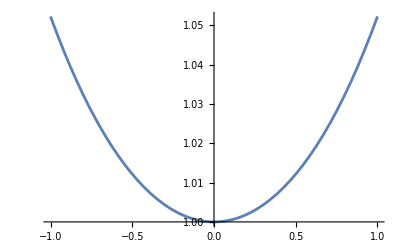

```mathematica
expr=Total@MapIndexed[{coeff,index}|->
2π coeff Total@Table[Integrate[RealSphericalHarmonicY[l,0,ArcCos[zi],0]zi^(index[[1]]-1) RealSphericalHarmonicY[l,0,ArcCos[z],0],{zi,-1,1}],{l,0,Length@moments+2}],moments]
Plot[expr,{z,-1,1}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000121176}

{1.,0.,0.0473674,0.,0.00492307,0.,-1.7053×10^-13,0.,0.,0.,-1.7053×10^-13,0.,-1.13687×10^-13}

{1,0,0.0473674,0,0.00492307}

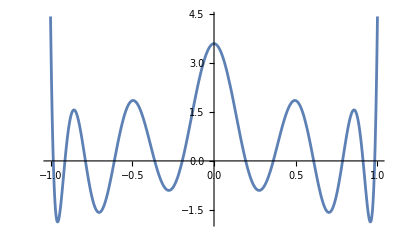

```mathematica
expr=LegendreP[0,z]/2+
15/4(0.0473674061-0.3333333333333333)LegendreP[2,z]+
315/16(0.0049230735+0.045113651914285624)LegendreP[4,z]+
1/0.010656010656010656(-0.006827664554112656)LegendreP[6,z]+
1/0.0023401435166141050.0014660400418025077LegendreP[8,z]+
1/0.0005278519210407755(-0.001011319471483585)LegendreP[10,z]+
1/0.00012117644100414326(0.0007193864642793812)LegendreP[12,z];
Table[N@Integrate[LegendreP[12,z] z^l,{z,-1,1}],{l,0,12}]
Table[N@Integrate[expr z^l,{z,-1,1}],{l,0,12}]
moments
Plot[expr,{z,-1,1}]
```

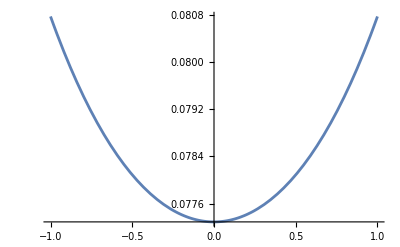

```mathematica
moments={1,0,4.73674061*^-02,0,4.92307350*^-3};
MyFun[z]:=Total@Flatten[MapIndexed[{mi,index}|->KeyValueMap[{key,value}|->mi value RealSphericalHarmonicY[key[[1]],key[[2]],ArcCos[z],0],  cartesianToSpherical[{0,0,index[[1]]-1}]],moments],1]
expr=MyFun[z];
Plot[expr,{z,-1,1}]
```

0.078321+0.00125646 (-1+3 z^2)-1.46367×10^-18 (3-30 z^2+35 z^4)-2.74845×10^-17 (-5+105 z^2-315 z^4+231 z^6)

0.078321+0.00125646 (-1+3 z^2)

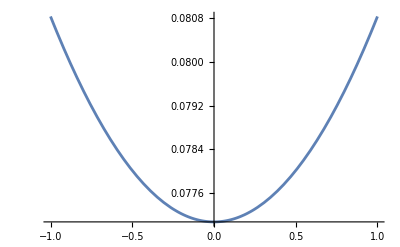

```mathematica
reconstruction=Total@Map[param|->param[[2]]LegendreP[param[[1]],z](2param[[1]]+1)/2,momentsSpherical]
true=MyFun[z]
Plot[{true(*,reconstruction*)},{z,-1,1}]
```

{1.,0,0.0473674}

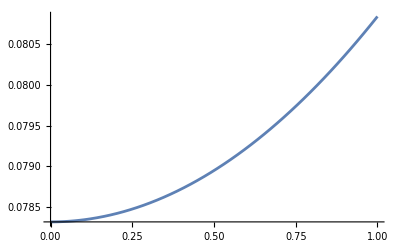

```mathematica
moments={1.00000000,0, 4.73674061*^-02}
expr=TransformedField["Spherical"->"Cartesian",
Total@Flatten[MapIndexed[{mi,index}|->KeyValueMap[{key,value}|-> mi value r^key[[1]] RealSphericalHarmonicY[key[[1]],key[[2]],θ,0],  cartesianToSpherical[{0,0,index[[1]]-1}]],moments],1],
{r,θ,ϕ}->{x,y,z}]/.{x->0,y->0}//Simplify;
Plot[expr,{z,0,1}(*,PlotRange->{Automatic,{-.03,.03}}*)]
```

```mathematica
expr=TransformedField["Spherical"->"Cartesian",
Total@Flatten[MapIndexed[
{coeff,l0}|->KeyValueMap[{lm,coeffLm}|->Factorial[l0[[1]]-1]coeffLm coeff r^(l0[[1]]-1)RealSphericalHarmonicY[l0[[1]]-1,0,θ,ϕ],cartesianToSpherical[{0,0,l0[[1]]-1}]],
moments],2],
{r,θ,ϕ}->Rx]/.{x->0,y->0};
Plot[expr,{z,0,4*^3/3*^8}(*,PlotRange->{0,0.0323}*)]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[moments,2].

TransformedField::nocoord: Rx is not a non-empty list of valid variables.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[moments,2.].

TransformedField::nocoord: Rx is not a non-empty list of valid variables.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[moments,2.].

TransformedField::nocoord: Rx is not a non-empty list of valid variables.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[moments,2.].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

TransformedField::nocoord: Rx is not a non-empty list of valid variables.

General::stop: Further output of TransformedField::nocoord will be suppressed during this calculation.

-Graphics-

```mathematica
Table[Integrate[LegendreP[3,Cos[θ]]LegendreP[l,Cos[θ]] Sin[θ],{θ,0,π}],{l,0,10}]
(*Norm: 2/(2l+1)*)
```

{0,0,0,2/7,0,0,0,0,0,0,0}

{0.284197,0.,3.79562,0.,2.16236,0.,1.15495,0.,-1.88829,0.,-5.60343,0.,-9.14882,0.,-12.2055,0.,-14.7096,0.,-16.6997,0.,-18.2477}

{0.284197,0.,3.80133,0.,2.18572,0.,1.14734,0.,-2.23173}

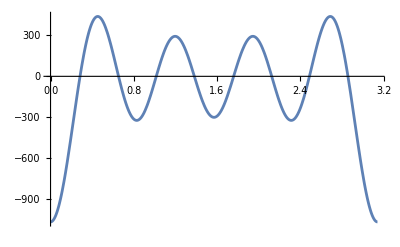

```mathematica
ct=Cos[θ];
expr=LegendreP[0,ct]/2 0.28419654+
LegendreP[2,ct]/2 5 (3.80132628+1.75)+
LegendreP[4,ct]/2 7 (-6)+
LegendreP[6,ct]/2 7 (-2)+
LegendreP[8,ct]/2 7 (-300);
Table[Integrate[Cos[θ]^l expr Sin[θ],{θ,0,π}],{l,0,20}]
moments
Plot[expr,{θ,0,π},PlotRange->All]
```

```mathematica
singleMom[l_]:=Module[{y},
y=D[Exp[-1/2(z/.001/(l+1)^2)^2],{z,l}];
y/Integrate[z^l y,{z,-∞,∞}]
]
expr=Total@MapIndexed[{mi,li}|->mi singleMom[li[[1]]-1],moments];
(*expr=moments[[1]]singleMom[0]+moments[[3]]singleMom[2]+moments[[5]]singleMom[4]+moments[[7]]singleMom[6];*)
Table[N@Integrate[z^l expr,{z,-∞,∞}],{l,0,12}]
moments
```

{0.284197,0.,3.80133,0.,2.18757,0.,1.16783,0.,-2.15441,0.,-0.654738,0.,-0.142442}

{0.284197,0.,3.80133,0.,2.18572,0.,1.14734,0.,-2.23173}

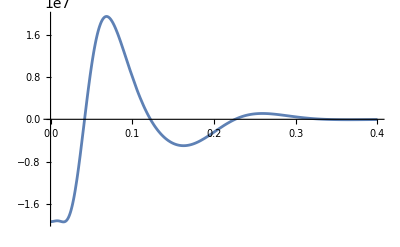

```mathematica
Plot[{expr},{z,0,.4},PlotRange->All]
```